6.

a)

```mathematica
NSolve[x^4 + x^3 + x^2 + x == 10, x]
```

{{x→-2.},{x→-0.201314-1.87729 ⅈ},{x→-0.201314+1.87729 ⅈ},{x→1.40263}}

b)

```mathematica
nofprimes[n_,m_]:=Length[Select[Table[k,{k,n,n+m}],PrimeQ]]
```

```mathematica
nofprimes[10^12,10^3]
```

37

c)

```mathematica
Integrate[x^2 Log[1+x]/Sqrt[x+2], {x,0,1}]
```

2/225 (1022 √2-942 √3-1290 ArcTanh[√2]+1290 ArcTanh[√3]+405 √3 Log[2])

7.

a)

L(x) = Coth(x)-1/x
Coth(x) ≃ 1/x + x/3 - x^3/45 +...
L(x) ≃x/3 -x^3/45
m = m/(3T) - m^3/(45 T^3)
45 T^3-15 T^2= -m^2

```mathematica
FindRoot[0 == 45T^3 -15T^2,{T, 1/2}]
```

{T→0.333333}

b)

FindRoot::precw: The precision of the argument function (-m^2 == -0.00001526098418826736`) is less than WorkingPrecision (50.).

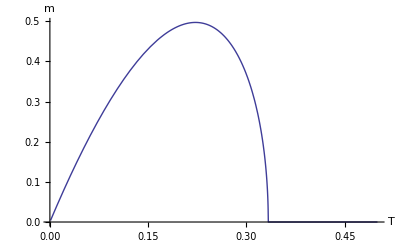

```mathematica
Plot[{m/.FindRoot[-m^2 == 45T^3 -15T^2,{m, 0.4},WorkingPrecision->50]},{T,0.001, 0.5}, AxesLabel -> {"T", "m"} ]
```

In part a) coth(x) is represented as a series expansion around x = 0, then m^2is solved for in terms of T. T_c occurs at m = 0, so FindRoot is used to solve the resulting equation to determine T_c. In part b) m is plotted against T and we see that m is positive between T = 0 and T = T_c and 0 for T > T_c

8.

a)

```mathematica
f[x_] := λ x(1-x^2);
```

```mathematica
fp[x_] :=D[f[x], x];
```

```mathematica
Solve[{1== λ(1-x^2), Abs[fp[x]] == 1}, {x,λ}]
```

{{λ→1,x→0},{λ→2,x→-1/(√2)},{λ→2,x→1/(√2)}}

f[x] and its derivative fp[x] are defined using the given map from x_n to x_(n+1). The equations x = f[x] and |fp[x]| = 1 are solved for analytically with the Solve function. It returns three solution but we are concerned with the one for x = 0. The fixed point there becomes unstable above λ = 1.

c)

```mathematica
f2[x_] := f[f[x]];
```

```mathematica
f4[x_] := f2[f2[x]];
```

```mathematica
f8[x_] := f4[f4[x]];
```

```mathematica
λ = 1.6;
```

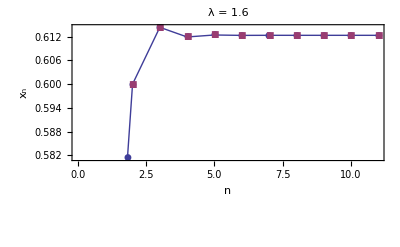

```mathematica
ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotRange -> Automatic, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 1.6" ]
```

```mathematica
FixedPoint[f, 0.5 , SameTest -> (Abs[#1 - #2] < 10^-11 &)]
```

0.612372

```mathematica
λ = 2.25;
```

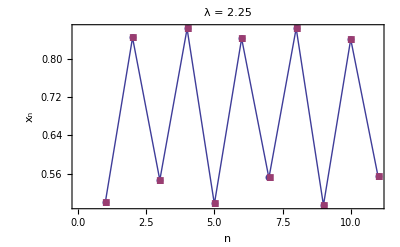

```mathematica
ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotRange -> Automatic, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 2.25" ]
```

```mathematica
FixedPoint[f4, 0.5 , SameTest -> (Abs[#1 - #2] < 10^-11 &)]
```

0.48942

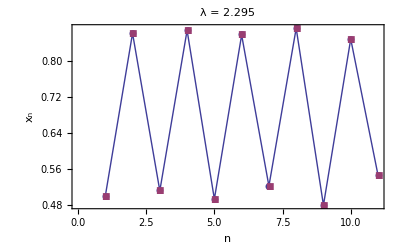

```mathematica
λ=2.295;
ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotRange -> Automatic, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 2.295" ]
```

```mathematica
FixedPoint[f8, 0.5 , SameTest -> (Abs[#1 - #2] < 10^-11 &)]
```

0.44544

```mathematica
λ = 2.34;
```

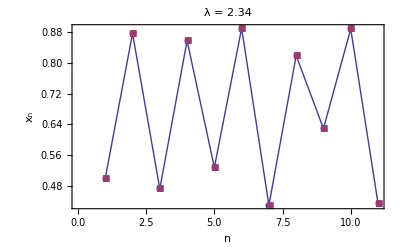

```mathematica
ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotRange -> Automatic, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 2.34" ]
```

```mathematica
lya [l_, xinit_, n_, ndrop_] := (λ = l;xlist =Drop[  NestList[f,xinit,  n] ,  ndrop+1 ]; 
Apply[ Plus, Log[ Abs[ f'[xlist] ] ] ] / Length[xlist])
```

```mathematica
lya[2.34,0.5, 10000, 100]
```

0.214403

For λ = 1.6 the graph of subsequent iterations clearly shows x approaching a fixed point. FixedPoint is used to find the numerical value of the fixed point. For λ = 2.25 there is a period 4 limit cycle evident in the plot; FixedPoint is used to find the fixed point for f4[x]. The plot for λ = 2.295 shows limit cycle but it is unclear to me that it is any specific number; FixedPoint found a fixed point of f8[x], while the other iterates didn't converge, so it must be a limit cycle of period 8. For λ = 2.34 the plot looks chaotic; the Lyapunov exponent was calculated to be positive, which confirms that it is chaotic.

d)

```mathematica
λ = 12/5;
```

```mathematica
x0 = N[4/5, 3000];
```

```mathematica
x1 = AccountingForm[f[x0], 5]
```

0.69120

```mathematica
x10 = AccountingForm[Nest[f, x0, 10],5]
```

0.85948

```mathematica
x5000 = AccountingForm[Nest[f, x0, 5000],5]
```

0.83601

The function Nest is used to iterate f[x] and AccountingForm is used to display only 5 decimal places. x0 was given a precision of 3000 to preserve the accuracy of the result for the 5000th iteration.

9.

a)

```mathematica
Clear[x]
```

```mathematica
V0 = 40;
```

```mathematica
V[x_] := (-V0/2)(1+Cos[Pi x])/; Abs[x] ≤  1;
```

```mathematica
V[x_] := 0 /; Abs[x] > 1;
```

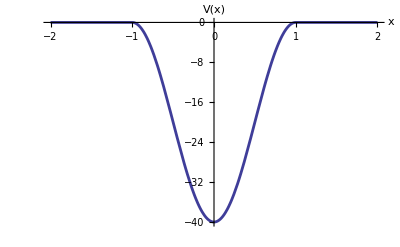

```mathematica
Plot[V[x], {x, -2, 2}, PlotStyle -> AbsoluteThickness[2], AxesLabel->{"x", "V(x)"}]
```

b)

```mathematica
B= 1;
```

```mathematica
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
```

```mathematica
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] := (en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-1/2] == ψ1[-1/2], 
					ψ2'[-1/2] == ψ1'[-1/2]}, 
		ψ2, {x, -1/2, 0} ])
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A= B;
```

```mathematica
evalue=energy /. FindRoot[sol2prime[0,energy],{energy,-40}]
```

-33.1411

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[evalue][[1]];
```

```mathematica
ψ [x_] := efunc2 [x] /;-1/2 ≤ x ≤ 0
```

```mathematica
ψ [x_] := efunc2 [-x] /;0 ≤ x ≤ 1/2
```

```mathematica
ψ [x_] := ψ1[x] /; x < -1/2
```

```mathematica
ψ [x_] := ψ3[x]/; x > 1/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψ[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψnorm[x_] := ψ[x] / normconst
```

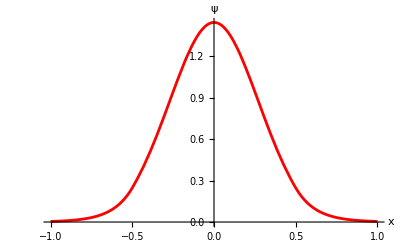

```mathematica
fig = Plot[ψnorm[x], {x, -1, 1}, AxesLabel -> {"x", "ψ"}, PlotStyle -> {Red, AbsoluteThickness[2]} ]
```

```mathematica
B = -A;
```

```mathematica
evalue = en /. FindRoot [sol2[0, en] ,{en, -40} ]
```

-19.2866

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[evalue][[1]];
```

```mathematica
ψ[x_] := -efunc2[-x] /; 0 ≤  x  ≤  1/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψ[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψnorm[x_] := ψ[x] / normconst
```

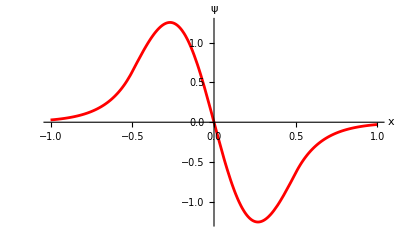

```mathematica
fig2 = Plot[ψnorm[x], {x, -1, 1}, AxesLabel -> {"x", "ψ"}, PlotStyle -> {Red, AbsoluteThickness[2]} ]
```

```mathematica
B = A;
```

```mathematica
evalue=energy /. FindRoot[sol2prime[0,energy],{energy,-10}]
```

-5.1394

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[evalue][[1]];
```

```mathematica
ψ [x_] := efunc2 [-x] /;0 ≤ x ≤ 1/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψ[x]^2, {x, -Infinity,Infinity} ] ];
```

```mathematica
ψnorm[x_] := ψ[x] / normconst
```

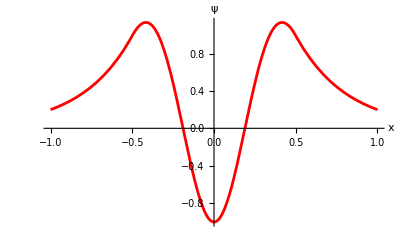

```mathematica
fig3= Plot[ψnorm[x], {x, -1, 1}, AxesLabel -> {"x", "ψ"}, PlotStyle -> {Red, AbsoluteThickness[2]} ]
```

```mathematica
B=A;
```

```mathematica
evalue4=energy /. FindRoot[sol2prime[0,energy],{energy,0}]
```

65.4499

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[evalue4][[1]];
```

```mathematica
ψ [x_] := efunc2 [-x] /;0 ≤ x ≤ 1/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψ[x]^2, {x, -Infinity,Infinity} ] ];
```

```mathematica
ψnorm[x_] := ψ[x] / normconst
```

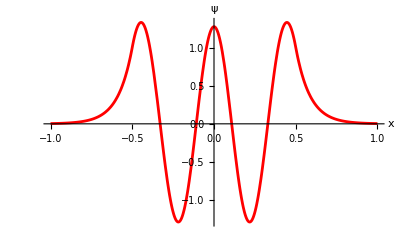

```mathematica
fig4= Plot[ψnorm[x], {x, -1, 1}, AxesLabel -> {"x", "ψ"}, PlotStyle -> {Red, AbsoluteThickness[2]} ]
```

The first four energy eigenvalues were found to be roughly -33, -19, -5 and 65. The corresponding wavefunctions were graphed. The lowest energy state is the ground state at -33, because the wavefunction has no nodes. The second state corresponds to an energy of -19; it is the first excited state with one node. The third excited state is at -5 and is even again, with 2 nodes. FindRoot was not able to find any more bound states; the next state it finds is at energy equal to 65 and the resulting wavefunction is even and has 4 nodes.